```mathematica
data={
{690.8,1.6129},
{623.4, 1.6172},
{579.1, 1.62},
{577, 1.621},
{546.1, 1.6238},
{491.6, 1.6311},
{435.8, 1.6411},
{407.8, 1.6492},
{404.7, 1.6506}
};
```

```mathematica
model =c /x^2+k;
fit=FindFit[data,model,{c,k},x]
```

{c→9347.3,k→1.59276}

```mathematica
ffit=model/.fit;
pfit=Plot[ffit,{x,400,700}];
```

```mathematica
pdata=ListPlot[data,PlotMarkers->Automatic];
```

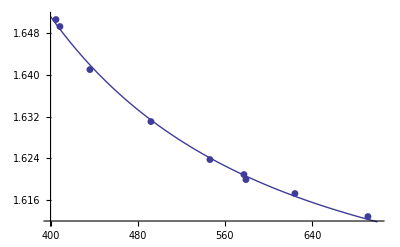

```mathematica
Show[pfit,pdata,PlotRange->All]
```

```mathematica
gelb1=ffit/.{x->579.1}
```

1.62063

```mathematica
gelb2=ffit/.{x->577.0}
```

1.62083

```mathematica
df=D[ffit,x]
```

-18694.6/x^3

```mathematica
df/.{x->579.1}
```

-0.0000962621

```mathematica
df/.{x->577.0}
```

-0.000097317